```mathematica
initial={0.01,0.1};
paraset=Import[FileNameJoin[{NotebookDirectory[],"paraset.csv"}]];
gElist={0.0025,0.005,0.01,0.025,0.05,0.1,0.2,0.3};
ListPlot[Sort@gElist];
ListPlot[Sort@Log10@gElist];
```

```mathematica
t1=AbsoluteTime[];
grlist={};
model=10^(Log10[80]+(Log10[1600]-Log10[80])*Exp[-Exp[x0*(t-dx)]]);
Mixinglist={};
growlist={};
timelist={};
Do[
SetDirectory[FileNameJoin[{NotebookDirectory[],"0.01","nonmotile","Dis1","data"<>ToString@j,"celldata"}]];
cellfile=FileNames[];
time=Sort@Table[ToExpression@StringDrop[StringDrop[cellfile[[k]],10],-4],{k,1,Length@cellfile}];
cellcount={};
mixlist={};
Do[
(*celldata=Import[FileNameJoin[{NotebookDirectory[],"0.01","Dis"<>ToString@i<>".zip"}],FileNameJoin[{"Dis"<>ToString@i,"data"<>ToString@j,"celldata","CellMatrix"<>ToString@time[[k]]<>".csv"}]];*)
celldata=Import[FileNameJoin[{NotebookDirectory[],"0.01","nonmotile","Dis1","data"<>ToString@j,"celldata","CellMatrix"<>ToString@time[[k]]<>".csv"}]];
cellnum=Length@celldata;
cellcount=Join[cellcount,{cellnum}];

celltype1=Select[celldata,#[[6]]==0&];
celltype2=Select[celldata,#[[6]]==1&];

Pos1=Take[celltype1,All,{2,3}];
Pos2=Take[celltype2,All,{2,3}];
distres=5;
nearA=Nearest[Pos1->"Index",DistanceFunction->EuclideanDistance];
nearB=Nearest[Pos2->"Index",DistanceFunction->EuclideanDistance];
(*对每个 A 细胞统计*)
mixinglist=Table[With[{pos=Pos1[[i]]},
(*找到在范围内的 A、B 细胞个数*)na=Length@nearA[pos,{All,distres}];
nb=Length@nearB[pos,{All,distres}];
If[na>0,N[nb/na],0]],{i,Length@Pos1}];
mixingindex=Mean[mixinglist];
mixlist=Join[mixlist,{mixingindex}];
t2=AbsoluteTime[];
If[Divisible[k,200]==True,Print["data No."<>ToString@j<>" time: "<>ToString@k<>" min finished! "<>ToString[t2-t1]<>"s used"]];
,{k,1,Length@time}];
fit=NonlinearModelFit[fitcount,model,{x0,dx},t];
fasttp=dx/.fit["BestFitParameters"];
Mumax=fit'[fasttp];
grlist=Join[grlist,{Mumax}];
growlist=Join[growlist,{cellcount}];
timelist=Join[timelist,{time}];
,{j,1,8}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"sumdata","intermixng-nonmotile-0.01.xlsx"}],Mixinglist];
Export[FileNameJoin[{NotebookDirectory[],"sumdata","GR-nonmotile-0.01.xlsx"}],grlist];
Export[FileNameJoin[{NotebookDirectory[],"sumdata","GRcurve-nonmotile-0.01.xlsx"}],growlist];
```

```mathematica
timelist={};
Do[
SetDirectory[FileNameJoin[{NotebookDirectory[],"0.005","nonmotile","Dis1","data"<>ToString@j,"celldata"}]];
cellfile=FileNames[];
time=Sort@Table[ToExpression@StringDrop[StringDrop[cellfile[[k]],10],-4],{k,1,Length@cellfile}];
timelist=Join[timelist,{time}];
,{j,1,8}];
Export[FileNameJoin[{NotebookDirectory[],"sumdata","time-nonmotile-0.005.xlsx"}],timelist];
```

```mathematica
t1=AbsoluteTime[];
partnerlist={};(*the number of partner/the rest of local space*)
timelist={};
Do[
SetDirectory[FileNameJoin[{NotebookDirectory[],"0.025","motile-QS","Dis1","data"<>ToString@j,"celldata"}]];
cellfile=FileNames[];
time=Sort@Table[ToExpression@StringDrop[StringDrop[cellfile[[k]],10],-4],{k,1,Length@cellfile}];
timelist=Join[timelist,{time}];
plist={};
Do[
(*celldata=Import[FileNameJoin[{NotebookDirectory[],"0.01","Dis"<>ToString@i<>".zip"}],FileNameJoin[{"Dis"<>ToString@i,"data"<>ToString@j,"celldata","CellMatrix"<>ToString@time[[k]]<>".csv"}]];*)
celldata=Import[FileNameJoin[{NotebookDirectory[],"0.025","motile-QS","Dis1","data"<>ToString@j,"celldata","CellMatrix"<>ToString@time[[k]]<>".csv"}]];
celltype1=Select[celldata,#[[6]]==0&];
celltype2=Select[celldata,#[[6]]==1&];

Pos1=Take[celltype1,All,{2,3}];
Pos2=Take[celltype2,All,{2,3}];
distres=5;
neighborhood=Count[Flatten@Table[If[EuclideanDistance[{x,y},{0,0}]<=distres,1,Nothing],{x,-distres,distres},{y,-distres,distres}],1];
nearA=Nearest[Pos1->"Index",DistanceFunction->EuclideanDistance];
nearB=Nearest[Pos2->"Index",DistanceFunction->EuclideanDistance];
(*对每个 A 细胞统计*)
partnerindex=Table[With[{pos=Pos1[[i]]},
(*找到在范围内的 A、B 细胞个数*)na=Length@nearA[pos,{All,distres}];
nb=Length@nearB[pos,{All,distres}];
N[nb/neighborhood]],{i,Length@Pos1}];
partnerindex1=Mean[partnerindex];
plist=Join[plist,{partnerindex1}];
t2=AbsoluteTime[];
If[Divisible[k,200]==True,Print["data No."<>ToString@j<>" time: "<>ToString@k<>" min finished! "<>ToString[t2-t1]<>"s used"]];
,{k,1,Length@time}];
partnerlist=Join[partnerlist,{plist}];
,{j,1,8}];
Export[FileNameJoin[{NotebookDirectory[],"sumdata","time-motileQS-0.025.xlsx"}],timelist];
Export[FileNameJoin[{NotebookDirectory[],"sumdata","partnerindex-motileQS-0.025.xlsx"}],partnerlist];
```

data No.1 time: 200 min finished! 7.6633216s used

data No.1 time: 400 min finished! 16.0159260s used

data No.1 time: 600 min finished! 25.2563853s used

data No.1 time: 800 min finished! 35.4927613s used

data No.1 time: 1000 min finished! 46.9404024s used

data No.2 time: 200 min finished! 55.3455277s used

data No.2 time: 400 min finished! 65.2329601s used

data No.2 time: 600 min finished! 76.3546656s used

data No.2 time: 800 min finished! 88.6317028s used

data No.3 time: 200 min finished! 112.0931345s used

data No.3 time: 400 min finished! 124.3744594s used

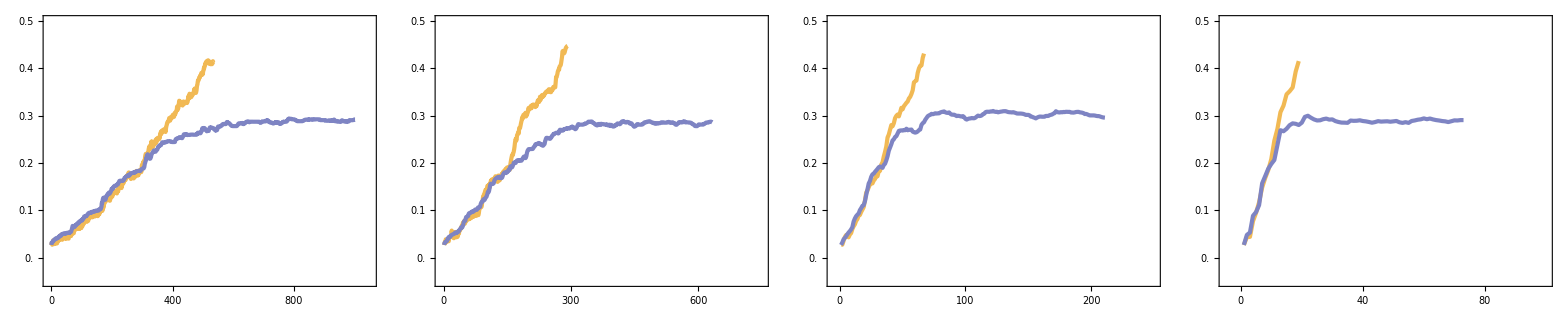

```mathematica
(*partner curve*)
partnerM1=ToExpression@First@Import[FileNameJoin[{NotebookDirectory[],"sumdata","partnerindex-motile-0.025.xlsx"}]];
partnerM1=Table[DeleteCases[partnerM1[[i]],Null],{i,1,8}];
ListLinePlot[partnerM1,ImageSize->300,AspectRatio->0.75,PlotRange->{{-50,1000},{-0.05,0.5}},
PlotStyle->Directive[Thickness[0.005],ColorData[95]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.5,0.1],None},{{#,#,{0.02,0}}&/@Range[0,1000,200],None}}];
partnerNM1=ToExpression@First@Import[FileNameJoin[{NotebookDirectory[],"sumdata","partnerindex-nonmotile-0.025.xlsx"}]];
partnerNM1=Table[DeleteCases[partnerNM1[[i]],Null],{i,1,8}];
ListLinePlot[partnerNM1,ImageSize->300,AspectRatio->0.75,PlotRange->{{-50,1050},{-0.05,0.5}},
PlotStyle->Directive[Thickness[0.005],ColorData[95]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.5,0.1],None},{{#,#,{0.02,0}}&/@Range[0,1000,200],None}}];
examplecurve=Grid[{{ListLinePlot[{partnerM1[[1]],partnerNM1[[1]]},ImageSize->300,AspectRatio->1,PlotRange->{{-5,1050},{-0.05,0.5}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.5,0.1],None},{{#,#,{0.02,0}}&/@Range[0,1050,200],None}}],
ListLinePlot[{partnerM1[[2]],partnerNM1[[2]]},ImageSize->300,AspectRatio->1,PlotRange->{{-5,750},{-0.05,0.5}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.5,0.1],None},{{#,#,{0.02,0}}&/@Range[0,750,150],None}}],
ListLinePlot[{partnerM1[[4]],partnerNM1[[4]]},ImageSize->300,AspectRatio->1,PlotRange->{{-5,250},{-0.05,0.5}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.5,0.1],None},{{#,#,{0.02,0}}&/@Range[0,250,50],None}}],
ListLinePlot[{partnerM1[[6]],partnerNM1[[6]]},ImageSize->300,AspectRatio->1,PlotRange->{{-5,100},{-0.05,0.5}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.5,0.1],None},{{#,#,{0.02,0}}&/@Range[0,100,20],None}}]}},Spacings->{1.5, 1}]
```

{3160,1560,790,320,180,90,50,30}

FittedModel[…]

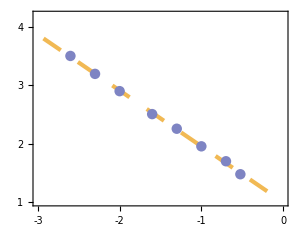

0.999154

```mathematica
partnerNM11=Table[partnerNM1[[i,1;;Length@partnerM1[[i]]]],{i,1,8}];
diff=partnerM1-partnerNM11;
diffp=Table[Select[diff[[i]],#<0&],{i,1,8}];
diffpos=Flatten@Table[If[diffp[[i]]=={},2*(9-i),Position[diff[[i]],diffp[[i]][[-1]]]],{i,1,8}]*10
plotdata1=Transpose@Join[{Log10@gElist},{Log10@diffpos}];
fit1=LinearModelFit[plotdata1,x,x]
plot1=Show[Plot[fit1[x],{x,-3.5,0.5},ImageSize->300,AspectRatio->0.75,PlotRange->{{-3,0},{1,4.2}},PlotStyle->Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255],Dashing[0.05]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[1,4,1],None},{{#,#,{0.02,0}}&/@Range[-3,0,1],None}}],ListPlot[plotdata1,PlotStyle->Directive[PointSize[0.025],RGBColor[126/255,132/255,195/255]]]]
fit1["AdjustedRSquared"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plot","GEsum-random-0.01.eps"}],plot1];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plot","example.eps"}],examplecurve];
Export[FileNameJoin[{NotebookDirectory[],"plot","GEsum-random.eps"}],plot1];
```

ListLinePlot::lpn: partnerQ1 不是由数字或者数对组成的列表.

ListLinePlot[partnerQ1,ImageSize→300,AspectRatio→0.75,PlotRange→{{-50,1100},{-0.05,0.5}},PlotStyle→Directive[Thickness[0.005],ColorDataFunction[…]],Frame→True,FrameStyle→Directive[Thickness[0.008],GrayLevel[0],18],Axes→False,FrameTicks→{{{{0.,0.,{0.02,0}},{0.1,0.1,{0.02,0}},{0.2,0.2,{0.02,0}},{0.3,0.3,{0.02,0}},{0.4,0.4,{0.02,0}},{0.5,0.5,{0.02,0}}},None},{{{0,0,{0.02,0}},{200,200,{0.02,0}},{400,400,{0.02,0}},{600,600,{0.02,0}},{800,800,{0.02,0}},{1000,1000,{0.02,0}}},None}}]

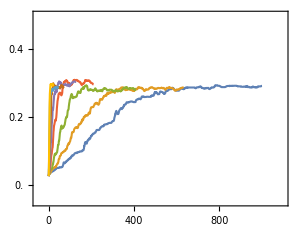

{}

```mathematica
ListLinePlot[partnerQ1,ImageSize->300,AspectRatio->0.75,PlotRange->{{-50,1100},{-0.05,0.5}},
PlotStyle->Directive[Thickness[0.005],ColorData[95]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.5,0.1],None},{{#,#,{0.02,0}}&/@Range[0,1000,200],None}}]
ListLinePlot[partnerNM1,ImageSize->300,AspectRatio->0.75,PlotRange->{{-50,1100},{-0.05,0.5}},
PlotStyle->Directive[Thickness[0.005],ColorData[95]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0,0.5,0.1],None},{{#,#,{0.02,0}}&/@Range[0,1000,200],None}}]
Table[{Length@partnerQ11[[i]],Length@partnerNM11[[i]]},{i,1,Length@partnerQ1}]
```

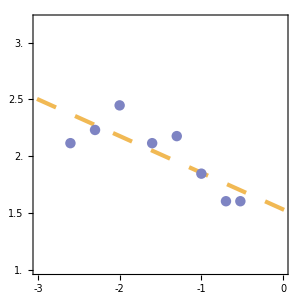

0.586916

```mathematica
partnerQ1=ToExpression@First@Import[FileNameJoin[{NotebookDirectory[],"sumdata","partnerindex-motileQS-0.025.xlsx"}]];
partnerQ1=Table[DeleteCases[partnerQ1[[i]],Null],{i,1,8}];
partnerNM1=ToExpression@First@Import[FileNameJoin[{NotebookDirectory[],"sumdata","partnerindex-nonmotile-0.025.xlsx"}]];
partnerNM1=Table[DeleteCases[partnerNM1[[i]],Null],{i,1,8}];
partnerQ11=Table[partnerQ1[[i,1;;Min[Length@partnerQ1[[i]],Length@partnerNM1[[i]]]]],{i,1,8}];
partnerNM11=Table[partnerNM1[[i,1;;Min[Length@partnerQ1[[i]],Length@partnerNM1[[i]]]]],{i,1,8}];
diff=partnerQ11-partnerNM11;
diffp=Table[Select[diff[[i]],#<0&],{i,1,8}];
diffpos=Flatten@Table[If[diffp[[i]]=={},65,Position[diff[[i]],diffp[[i]][[-1]]]],{i,1,8}]*10;
plotdata2=Transpose@Join[{Log10@gElist},{Log10@diffpos}];
fit2=LinearModelFit[plotdata2,x,x];
plot2=Show[Plot[fit2[x],{x,-3.5,0.5},ImageSize->300,AspectRatio->1,PlotRange->{{-3,0},{1,3.2}},PlotStyle->Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255],Dashing[0.05]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[1,3,0.5],None},{{#,#,{0.02,0}}&/@Range[-3,0,1],None}}],ListPlot[plotdata2,PlotStyle->Directive[PointSize[0.025],RGBColor[126/255,132/255,195/255]]]]
fit2["AdjustedRSquared"]
Export[FileNameJoin[{NotebookDirectory[],"plot","GEsum-QS.eps"}],plot2];
```

{50,50,50,50,50,50,20,50}

FittedModel[…]

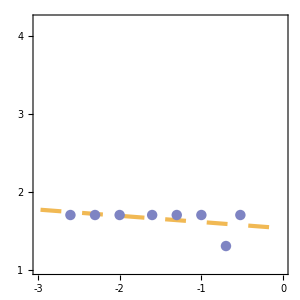

0.0489563

```mathematica
partnerM2=ToExpression@First@Import[FileNameJoin[{NotebookDirectory[],"sumdata","partnerindex-motileQS-0.1.xlsx"}]];
partnerM2=Table[DeleteCases[partnerM2[[i]],Null],{i,1,8}];
partnerNM2=ToExpression@First@Import[FileNameJoin[{NotebookDirectory[],"sumdata","partnerindex-nonmotile-0.1.xlsx"}]];
partnerNM2=Table[DeleteCases[partnerNM2[[i]],Null],{i,1,8}];
partnerM21=Table[partnerM2[[i,1;;Min[Length@partnerM2[[i]],Length@partnerNM2[[i]]]]],{i,1,8}];
partnerNM21=Table[partnerNM2[[i,1;;Min[Length@partnerM2[[i]],Length@partnerNM2[[i]]]]],{i,1,8}];
diff=partnerM21-partnerNM21;
diffp=Table[Select[diff[[i]],#<0&],{i,1,8}];
diffpos=Flatten@Table[If[diffp[[i]]=={},5,Position[diff[[i]],diffp[[i]][[-1]]]],{i,1,8}]*10
plotdata3=Transpose@Join[{Log10@gElist},{Log10@diffpos}];
fit3=LinearModelFit[plotdata3,x,x]
plot2=Show[Plot[fit3[x],{x,-3.5,0.5},ImageSize->300,AspectRatio->1,PlotRange->{{-3,0},{1,4.2}},PlotStyle->Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255],Dashing[0.05]],Frame->True,FrameStyle->Directive[Thickness[0.008],Black,18],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[1,4,1],None},{{#,#,{0.02,0}}&/@Range[-3,0,1],None}}],ListPlot[plotdata3,PlotStyle->Directive[PointSize[0.025],RGBColor[126/255,132/255,195/255]]]]
fit3["AdjustedRSquared"]
Export[FileNameJoin[{NotebookDirectory[],"plot","GEsum-random-0.1.eps"}],plot2];
```